### The Integrand in 3 Dimensions:

```mathematica
x[k_,l_]:=k*l
```

```mathematica
Subscript[R, x_][θ_]:=((1.334 * E^(-x/Cos[θ])*Cos[θ])/(1-1.334^2*(Sin[θ])^2)^(1/2))
```

```mathematica
f[z_]:=NIntegrate[2*Pi*Sin[θ]*Subscript[R, z][θ],{θ,0,ArcSin[1/1.334]}]/(2*Pi)
```

```mathematica
Subscript[f, 0]=f[0]
```

0.749625

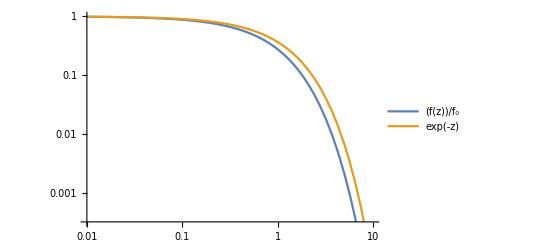

```mathematica
LogLogPlot[{f[z]/Subscript[f, 0],Exp[-z]},{z,0.01,10},PlotLegends->"Expressions"]
```

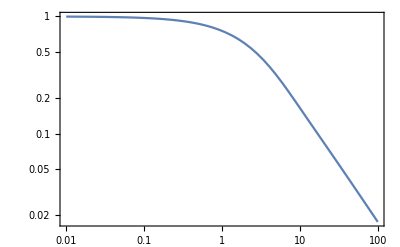

```mathematica
LogLogPlot[(f[z]/Subscript[f, 0])/Exp[-z],{z,0.01,100},Frame->True,GridLines->Automatic]
```

```mathematica
a= Series[Cos[x],{x,0,6}]
```

1-x^2/2+x^4/24-x^6/720+O[x]^7

```mathematica
b= Series[Sin[x],{x,0,7}]
```

x-x^3/6+x^5/120-x^7/5040+O[x]^8

```mathematica
c=Series[Exp[Cos[x]],{x,0,7}]
```

ⅇ-(ⅇ x^2)/2+(ⅇ x^4)/6-(31 ⅇ x^6)/720+O[x]^8

```mathematica
d=Exp[-1.334/a]
```

0.263421-0.175702 x^2-0.0146126 x^4+0.00603081 x^6+O[x]^7

```mathematica
e=(1.334*a)^2
```

1.77956-1.77956 x^2+0.593185 x^4-0.0790914 x^6+O[x]^7

```mathematica
integrand=(1.334*Pi*a*b*d)/(1-e)^0.5
```

(7.65621×10^-17-1.25035 ⅈ) x+(1.60054×10^-16+0.240413 ⅈ) x^3+(3.51055×10^-16-0.717689 ⅈ) x^5+(7.57894×10^-16-1.15189 ⅈ) x^7+O[x]^8

```mathematica
CoefficientList[integrand,x]
```

{0,7.65621×10^-17-1.25035 ⅈ,0,1.60054×10^-16+0.240413 ⅈ,0,3.51055×10^-16-0.717689 ⅈ,0,7.57894×10^-16-1.15189 ⅈ}

```mathematica
NIntegrate[(1.334*Pi*a*b*d)/(1-e)^0.5,{x,0,ArcSin[1/1.334]}]/(2*Pi)
```

NIntegrate::inumri: The integrand (7.65621×10^-17-1.25035 ⅈ) x+(1.60054×10^-16+0.240413 ⅈ) x^3+(3.51055×10^-16-0.717689 ⅈ) x^5+(7.57894×10^-16-1.15189 ⅈ) x^7+O[x]^8 has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0,0.847496}}.

NIntegrate[(1.334 π a b d)/(1-e)^0.5,{x,0,ArcSin[1/1.334]}]/(2 π)